# Definitions of functions. To be placed in separate files.

```mathematica
<<FeynCalc`
<<DummyArray`
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<ETensor`
<<CETensor`
<<GravitonVertex`
<<GravitonScalarVertex`
<<GravitonFermionVertex`
<<GravitonVectorVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## E tensor conjugated

The definition of the E tensor conjugated. It is responsible for the perturbative expansion of the vierbein.
(𝔢^m)_μ= (Σ_(n=0))^∞κ^n(1/2
n)I_m^(μρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)... h_(ρ_n σ_n) =(Σ_(n=0))^∞κ^n((E^m)_μ)^(ρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n) .

This expression also works for 𝔢_mμ:
𝔢_mμ= (Σ_(n=0))^∞κ^n(1/2
n)I_mμ^(ρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)... h_(ρ_n σ_n) =(Σ_(n=0))^∞κ^n E_mμ^(ρ_1 σ_1... ρ_n σ_n)h_(ρ_1 σ_1)...h_(ρ_n σ_n) .

```mathematica
ETensorC = {indexArrayExternal,indexArrayInternal}↦Expand[Binomial[1/2,Length[indexArrayInternal]/2]ITensor[Join[indexArrayExternal,indexArrayInternal]]];
```

Examples.

```mathematica
ETensorC[{μ,ν},{}]
ETensorC[{μ,ν},dummyArray[1]]
ETensorC[{α,β},dummyArray[2]]
```

g^μν

1/4 g^m1ν g^n1μ+1/4 g^m1μ g^n1ν

-1/64 g^m1β g^m2α g^n1n2-1/64 g^m1α g^m2β g^n1n2-1/64 g^m1n2 g^m2β g^n1α-1/64 g^m1n2 g^m2α g^n1β-1/64 g^m1β g^m2n1 g^n2α-1/64 g^m1m2 g^n1β g^n2α-1/64 g^m1α g^m2n1 g^n2β-1/64 g^m1m2 g^n1α g^n2β

## CE tensor conjugated

The definition of CE tensor conjugated. It is responsible for the perturbative expansion of the √-g 𝔢_mμ  factor.

The distribution of internal indices match the one generated for the CI tensor.

The distribution of all indices match the one generate for the CI tensor.

This cell gives CE tensor conjugated without all index symmetries.

```mathematica
CETensorCCore = {indexArrayExternal,indexArrayInternal}↦Total[Function[CTensor[#[[1]]] ETensorC[#[[2]][[;;2]],#[[2]][[3;;]]]  ]/@CITensorIndices[indexArrayExternal,indexArrayInternal]];
```

This cell gives the definition of CE tensor with all required symmetries.

```mathematica
CETensorC = {indexArrayExternal,indexArrayInternal}↦Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CETensorCCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]];
```

Examples

```mathematica
CETensorC[{μ,ν},{}]
CETensorC[{μ,ν},dummyArray[1]]
CETensorC[{μ,ν},dummyArray[2]]
```

g^μν

1/4 g^m1ν g^n1μ+1/4 g^m1μ g^n1ν+1/2 g^μν g^m1n1

-1/64 g^m1ν g^m2μ g^n1n2-1/64 g^m1μ g^m2ν g^n1n2-1/8 g^μν g^m1m2 g^n1n2+1/16 g^m1ν g^m2n2 g^n1μ-1/64 g^m1n2 g^m2ν g^n1μ+1/16 g^m1μ g^m2n2 g^n1ν-1/64 g^m1n2 g^m2μ g^n1ν-1/64 g^m1ν g^m2n1 g^n2μ+1/16 g^m1n1 g^m2ν g^n2μ-1/64 g^m1m2 g^n1ν g^n2μ-1/64 g^m1μ g^m2n1 g^n2ν+1/16 g^m1n1 g^m2μ g^n2ν-1/64 g^m1m2 g^n1μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2

## CI tensor conjugated

Here the definition of the CI tensor is given. The tensor is responsible for the perturbative structure of √-g g_μν.
N.B. the metric has low indices, so it admits a finite expansion.
The complete expansion is, however, infinite.

This cell generates a distributions of internal indices.

```mathematica
CITensorCInternalIndices=Function[indexArray,  FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],2],((Total[#]==n)&&(#[[2]]<=1))&])[Length[indexArray]/2]  ];
```

This cell generates a distribution of both internal and external indices.

```mathematica
CITensorCIndices=Function[{indexArrayExternal,indexArrayInternal},Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CITensorCInternalIndices[indexArrayInternal]  ];
```

This cell gives the definition of the CI tensor without all symmetries.

```mathematica
CITensorCCore = Function[{indexArrayExternal,indexArrayInternal},Total[  (indexArray↦CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CITensorCIndices[indexArrayExternal,indexArrayInternal]  ]  ];
```

This cell gives the definition of the CI tensor with symmetries.

```mathematica
CITensorC=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CITensorCCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]  ];
```

Examples

```mathematica
CITensorC[{μ,ν},{}]
CITensorC[{μ,ν},{m,n}]
CITensorC[{μ,ν},dummyArray[2]]
```

g^μν

1/2 g^mν g^nμ+1/2 g^mμ g^nν+1/2 g^μν g^mn

1/8 g^m1ν g^m2n2 g^n1μ+1/8 g^m1μ g^m2n2 g^n1ν+1/8 g^m1n1 g^m2ν g^n2μ+1/8 g^m1n1 g^m2μ g^n2ν-1/8 g^μν g^m1n2 g^m2n1+1/8 g^μν g^m1n1 g^m2n2-1/8 g^μν g^m1m2 g^n1n2

## CII tensor conjugated

Here the definition of the CII tensor is given. The tensor is responsible for the perturbative structure of √-g g_μν g_αβ.
N.B. metrics have low indices, so their expansions are finite! The overall expansion is infinite.

This cell gives the distribution of internal indices.

```mathematica
CIITensorCInternalIndices=Function[indexArray,FoldPairList[TakeDrop,indexArray,2#]&/@(n↦Select[Tuples[Range[0,n],3],((Total[#]==n)&&(#[[2]]<=1)&&(#[[3]]<=1))&])[Length[indexArray]/2]];
```

This cell gives the distribution of both internal and external indices.

```mathematica
CIITensorCIndices=Function[{indexArrayExternal,indexArrayInternal},Function[MapThread[Join,{Join[{{}},Partition[indexArrayExternal,2]],#}]]/@CIITensorCInternalIndices[indexArrayInternal]];
```

This cell gives the definition of the CII tensor without all index symmetries.

```mathematica
CIITensorCCore = Function[{indexArrayExternal,indexArrayInternal},Total[  (indexArray↦CTensor[indexArray[[1]]](Times@@ITensor/@indexArray[[2;;]]) )/@CIITensorCIndices[indexArrayExternal,indexArrayInternal]  ]];
```

The definition of the CII tensor with all index symmetries.

```mathematica
CIITensorC=Function[{indexArrayExternal,indexArrayInternal},Expand[Total[1/Factorial[Length[indexArrayInternal]/2](Function[CIITensorCCore[indexArrayExternal,#]]/@Flatten/@Permutations[Partition[indexArrayInternal,2]])]]];
```

Examples

```mathematica
CIITensorC[{μ,ν,α,β},{}]
CIITensorC[dummyArray[2],{μ,ν}]
CIITensorC[{μ,ν,ρ,σ},dummyArray[2]]
```

g^αβ g^μν

1/2 g^m1ν g^m2n2 g^n1μ+1/2 g^m1μ g^m2n2 g^n1ν+1/2 g^m1n1 g^m2ν g^n2μ+1/2 g^m1n1 g^m2μ g^n2ν+1/2 g^μν g^m1n1 g^m2n2

1/8 g^m1σ g^m2ν g^n1ρ g^n2μ+1/8 g^m1ρ g^m2ν g^n1σ g^n2μ+1/8 g^m1n1 g^m2ν g^n2μ g^ρσ+1/8 g^m1σ g^m2μ g^n1ρ g^n2ν+1/8 g^m1ρ g^m2μ g^n1σ g^n2ν+1/8 g^m1ν g^m2σ g^n1μ g^n2ρ+1/8 g^m1μ g^m2σ g^n1ν g^n2ρ+1/8 g^m1ν g^m2ρ g^n1μ g^n2σ+1/8 g^m1μ g^m2ρ g^n1ν g^n2σ+1/8 g^μν g^m1σ g^m2n2 g^n1ρ+1/8 g^μν g^m1ρ g^m2n2 g^n1σ+1/8 g^μν g^m1n1 g^m2σ g^n2ρ+1/8 g^μν g^m1n1 g^m2ρ g^n2σ+1/8 g^m1ν g^m2n2 g^n1μ g^ρσ+1/8 g^m1μ g^m2n2 g^n1ν g^ρσ+1/8 g^m1n1 g^m2μ g^n2ν g^ρσ-1/8 g^μν g^m1n2 g^m2n1 g^ρσ+1/8 g^μν g^m1n1 g^m2n2 g^ρσ-1/8 g^μν g^m1m2 g^n1n2 g^ρσ

## SU(N) Yang-Mills vertices gravitational interaction.

Here the gravitational interaction of gluon vertices is generated. 
It is generated directly by the FeynCalc code for the sake of consistency.

Quark-Gluon vertex.

```mathematica
GravitonQuarkGluonVertex=indexArray↦CETensorC[{indexArray[[Length[indexArray]-1]],𝓂},indexArray[[;;Length[indexArray]-2]]] QuarkGluonVertex[𝓂,Last[indexArray]]//Calc;
```

Examples.

```mathematica
GravitonQuarkGluonVertex[{μ,a}]==QuarkGluonVertex[μ,a]//Calc
GravitonQuarkGluonVertex[{α,β,μ,a}]
GravitonQuarkGluonVertex[{α,β,ρ,σ,μ,a}]
```

True

1/2 ⅈ T^a γ^μ g_s g^αβ+1/4 ⅈ T^a γ^β g_s g^αμ+1/4 ⅈ γ^α T^a g_s g^βμ

-1/64 ⅈ T^a γ^σ g_s g^αρ g^βμ-1/64 ⅈ T^a γ^ρ g_s g^ασ g^βμ-1/64 ⅈ T^a γ^σ g_s g^αμ g^βρ-1/8 ⅈ T^a γ^μ g_s g^ασ g^βρ-1/64 ⅈ T^a γ^ρ g_s g^αμ g^βσ-1/8 ⅈ T^a γ^μ g_s g^αρ g^βσ+1/16 ⅈ T^a γ^σ g_s g^αβ g^μρ-1/64 ⅈ T^a γ^β g_s g^ασ g^μρ-1/64 ⅈ γ^α T^a g_s g^βσ g^μρ+1/16 ⅈ T^a γ^ρ g_s g^αβ g^μσ-1/64 ⅈ T^a γ^β g_s g^αρ g^μσ-1/64 ⅈ γ^α T^a g_s g^βρ g^μσ+1/8 ⅈ T^a γ^μ g_s g^αβ g^ρσ+1/16 ⅈ T^a γ^β g_s g^αμ g^ρσ+1/16 ⅈ γ^α T^a g_s g^βμ g^ρσ

Three-Gluon Vertex.

```mathematica
GravitonThreeGluonVertex=Function[indexArray,GluonVertex[Sequence@@indexArray[[Length[indexArray]-8;;]],Explicit->True]/.Pair[LorentzIndex[𝓍_,D],LorentzIndex[𝓎_,D]]->CITensorC[{𝓍,𝓎},indexArray[[;;Length[indexArray]-9]]]//Calc];
```

Examples.

```mathematica
GravitonThreeGluonVertex[{p1,μ1,a,p2,μ2,b,p3,μ3,c}]==GluonVertex[p1,μ1,a,p2,μ2,b,p3,μ3,c]//Calc
GravitonThreeGluonVertex[{μ,ν,p1,μ1,a,p2,μ2,b,p3,μ3,c}]
GravitonThreeGluonVertex[{μ,ν,α,β,p1,μ1,a,p2,μ2,b,p3,μ3,c}]
```

True

-1/2 g_s p1^μ2 g^μν g^μ1μ3 f^abc-1/2 g_s p1^μ2 g^μμ3 g^μ1ν f^abc-1/2 g_s p1^μ2 g^μμ1 g^μ3ν f^abc+1/2 g_s p1^μ3 g^μν g^μ1μ2 f^abc+1/2 g_s p1^μ3 g^μμ2 g^μ1ν f^abc+1/2 g_s p1^μ3 g^μμ1 g^μ2ν f^abc+1/2 g_s p2^μ1 g^μν g^μ2μ3 f^abc+1/2 g_s p2^μ1 g^μμ3 g^μ2ν f^abc+1/2 g_s p2^μ1 g^μμ2 g^μ3ν f^abc-1/2 g_s p2^μ3 g^μν g^μ1μ2 f^abc-1/2 g_s p2^μ3 g^μμ2 g^μ1ν f^abc-1/2 g_s p2^μ3 g^μμ1 g^μ2ν f^abc-1/2 g_s p3^μ1 g^μν g^μ2μ3 f^abc-1/2 g_s p3^μ1 g^μμ3 g^μ2ν f^abc+1/2 g_s p3^μ2 g^μν g^μ1μ3 f^abc+1/2 g_s p3^μ2 g^μμ3 g^μ1ν f^abc-1/2 g_s p3^μ1 g^μμ2 g^μ3ν f^abc+1/2 g_s p3^μ2 g^μμ1 g^μ3ν f^abc

1/8 g^αμ3 g^βμ2 g^μν p2^μ1 g_s f^abc+1/8 g^αμ2 g^βμ3 g^μν p2^μ1 g_s f^abc-1/8 g^αμ3 g^βμ2 g^μν p3^μ1 g_s f^abc-1/8 g^αμ2 g^βμ3 g^μν p3^μ1 g_s f^abc-1/8 g^αν g^βμ p2^μ1 g^μ2μ3 g_s f^abc-1/8 g^αμ g^βν p2^μ1 g^μ2μ3 g_s f^abc+1/8 g^αβ g^μν p2^μ1 g^μ2μ3 g_s f^abc+1/8 g^αν g^βμ p3^μ1 g^μ2μ3 g_s f^abc+1/8 g^αμ g^βν p3^μ1 g^μ2μ3 g_s f^abc-1/8 g^αβ g^μν p3^μ1 g^μ2μ3 g_s f^abc+1/8 g^αβ g^μμ3 p2^μ1 g^μ2ν g_s f^abc-1/8 g^αβ g^μμ3 p3^μ1 g^μ2ν g_s f^abc-1/8 g^αμ3 g^βμ1 g^μν p1^μ2 g_s f^abc-1/8 g^αμ1 g^βμ3 g^μν p1^μ2 g_s f^abc+1/8 g^αν g^βμ g^μ1μ3 p1^μ2 g_s f^abc+1/8 g^αμ g^βν g^μ1μ3 p1^μ2 g_s f^abc-1/8 g^αβ g^μν g^μ1μ3 p1^μ2 g_s f^abc-1/8 g^αβ g^μμ3 g^μ1ν p1^μ2 g_s f^abc+1/8 g^αμ3 g^βμ1 g^μν p3^μ2 g_s f^abc+1/8 g^αμ1 g^βμ3 g^μν p3^μ2 g_s f^abc-1/8 g^αν g^βμ g^μ1μ3 p3^μ2 g_s f^abc-1/8 g^αμ g^βν g^μ1μ3 p3^μ2 g_s f^abc+1/8 g^αβ g^μν g^μ1μ3 p3^μ2 g_s f^abc+1/8 g^αβ g^μμ3 g^μ1ν p3^μ2 g_s f^abc+1/8 g^αβ g^μμ2 p2^μ1 g^μ3ν g_s f^abc-1/8 g^αβ g^μμ2 p3^μ1 g^μ3ν g_s f^abc-1/8 g^αβ g^μμ1 p1^μ2 g^μ3ν g_s f^abc+1/8 g^αβ g^μμ1 p3^μ2 g^μ3ν g_s f^abc+1/8 g^αμ2 g^βμ1 g^μν p1^μ3 g_s f^abc+1/8 g^αμ1 g^βμ2 g^μν p1^μ3 g_s f^abc-1/8 g^αν g^βμ g^μ1μ2 p1^μ3 g_s f^abc-1/8 g^αμ g^βν g^μ1μ2 p1^μ3 g_s f^abc+1/8 g^αβ g^μν g^μ1μ2 p1^μ3 g_s f^abc+1/8 g^αβ g^μμ2 g^μ1ν p1^μ3 g_s f^abc+1/8 g^αβ g^μμ1 g^μ2ν p1^μ3 g_s f^abc-1/8 g^αμ2 g^βμ1 g^μν p2^μ3 g_s f^abc-1/8 g^αμ1 g^βμ2 g^μν p2^μ3 g_s f^abc+1/8 g^αν g^βμ g^μ1μ2 p2^μ3 g_s f^abc+1/8 g^αμ g^βν g^μ1μ2 p2^μ3 g_s f^abc-1/8 g^αβ g^μν g^μ1μ2 p2^μ3 g_s f^abc-1/8 g^αβ g^μμ2 g^μ1ν p2^μ3 g_s f^abc-1/8 g^αβ g^μμ1 g^μ2ν p2^μ3 g_s f^abc

Four-Gluon Vertex.

```mathematica
GravitonFourGluonVertex=Function[indexArray, Explicit[GluonVertex[Sequence @@ indexArray[[Length[indexArray] - 11 ;;]]]] /. Pair[LorentzIndex[𝓍_, D], LorentzIndex[𝓎_, D]] Pair[LorentzIndex[𝒶_, D], LorentzIndex[𝒷_, D]] -> CIITensorC[{𝓍, 𝓎, 𝒶, 𝒷}, indexArray[[;; Length[indexArray] - 12]]]//Calc  ];
```

```mathematica
GravitonFourGluonVertex[{p1,μ1,a1,p2,μ2,a2,p3,μ3,a3,p4,μ4,a4}]
GluonVertex[p1,μ1,a1,p2,μ2,a2,p3,μ3,a3,p4,μ4,a4]//Calc
GravitonFourGluonVertex[{μ,ν,p1,μ1,a1,p2,μ2,a2,p3,μ3,a3,p4,μ4,a4}]
GravitonFourGluonVertex[{μ,ν,ρ,σ,p1,μ1,a1,p2,μ2,a2,p3,μ3,a3,p4,μ4,a4}]
```

ⅈ g_s^2 g^μ1μ3 g^μ2μ4 f^(a1a4FCGV(u2066)) f^(a2a3FCGV(u2066))-ⅈ g_s^2 g^μ1μ2 g^μ3μ4 f^(a1a4FCGV(u2066)) f^(a2a3FCGV(u2066))+ⅈ g_s^2 g^μ1μ4 g^μ2μ3 f^(a1a3FCGV(u2066)) f^(a2a4FCGV(u2066))-ⅈ g_s^2 g^μ1μ2 g^μ3μ4 f^(a1a3FCGV(u2066)) f^(a2a4FCGV(u2066))+ⅈ g_s^2 g^μ1μ4 g^μ2μ3 f^(a1a2FCGV(u2066)) f^(a3a4FCGV(u2066))-ⅈ g_s^2 g^μ1μ3 g^μ2μ4 f^(a1a2FCGV(u2066)) f^(a3a4FCGV(u2066))

ⅈ g_s^2 g^μ1μ3 g^μ2μ4 f^(a1a4FCGV(u2080)) f^(a2a3FCGV(u2080))-ⅈ g_s^2 g^μ1μ2 g^μ3μ4 f^(a1a4FCGV(u2080)) f^(a2a3FCGV(u2080))+ⅈ g_s^2 g^μ1μ4 g^μ2μ3 f^(a1a3FCGV(u2080)) f^(a2a4FCGV(u2080))-ⅈ g_s^2 g^μ1μ2 g^μ3μ4 f^(a1a3FCGV(u2080)) f^(a2a4FCGV(u2080))+ⅈ g_s^2 g^μ1μ4 g^μ2μ3 f^(a1a2FCGV(u2080)) f^(a3a4FCGV(u2080))-ⅈ g_s^2 g^μ1μ3 g^μ2μ4 f^(a1a2FCGV(u2080)) f^(a3a4FCGV(u2080))

1/2 ⅈ g^μν g^μ1μ3 g^μ2μ4 f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ3 g^μ1ν g^μ2μ4 f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ4 g^μ1μ3 g^μ2ν f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2-1/2 ⅈ g^μν g^μ1μ2 g^μ3μ4 f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ2 g^μ1ν g^μ3μ4 f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ1 g^μ2ν g^μ3μ4 f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ4 g^μ1μ2 g^μ3ν f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ1 g^μ2μ4 g^μ3ν f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ3 g^μ1μ2 g^μ4ν f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ2 g^μ1μ3 g^μ4ν f^(a1a4FCGV(u2089)) f^(a2a3FCGV(u2089)) g_s^2+1/2 ⅈ g^μν g^μ1μ4 g^μ2μ3 f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ4 g^μ1ν g^μ2μ3 f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ3 g^μ1μ4 g^μ2ν f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μν g^μ1μ2 g^μ3μ4 f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ2 g^μ1ν g^μ3μ4 f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ1 g^μ2ν g^μ3μ4 f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ4 g^μ1μ2 g^μ3ν f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ2 g^μ1μ4 g^μ3ν f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ3 g^μ1μ2 g^μ4ν f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ1 g^μ2μ3 g^μ4ν f^(a1a3FCGV(u2089)) f^(a2a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μν g^μ1μ4 g^μ2μ3 f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ4 g^μ1ν g^μ2μ3 f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μν g^μ1μ3 g^μ2μ4 f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ3 g^μ1ν g^μ2μ4 f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ4 g^μ1μ3 g^μ2ν f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ3 g^μ1μ4 g^μ2ν f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ2 g^μ1μ4 g^μ3ν f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ1 g^μ2μ4 g^μ3ν f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2-1/2 ⅈ g^μμ2 g^μ1μ3 g^μ4ν f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2+1/2 ⅈ g^μμ1 g^μ2μ3 g^μ4ν f^(a1a2FCGV(u2089)) f^(a3a4FCGV(u2089)) g_s^2

-1/8 ⅈ g^μν g^μ1σ g^μ2ρ g^μ3μ4 f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1ρ g^μ2σ g^μ3μ4 f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1σ g^μ2ρ g^μ3ν f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1ρ g^μ2σ g^μ3ν f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1σ g^μ2μ4 g^μ3ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1σ g^μ2ν g^μ3ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1ρ g^μ2μ4 g^μ3σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ρ g^μ2ν g^μ3σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1σ g^μ2ρ g^μ4ν f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1ρ g^μ2σ g^μ4ν f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1σ g^μ3ρ g^μ4ν f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1ρ g^μ3σ g^μ4ν f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ3 g^μ2σ g^μ4ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1ν g^μ2σ g^μ4ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2σ g^μ3ν g^μ4ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ2 g^μ3σ g^μ4ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ν g^μ3σ g^μ4ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ν g^μ3σ g^μ4ρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ3 g^μ2ρ g^μ4σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1ν g^μ2ρ g^μ4σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2ρ g^μ3ν g^μ4σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ2 g^μ3ρ g^μ4σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ν g^μ3ρ g^μ4σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ν g^μ3ρ g^μ4σ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μσ g^μ1μ3 g^μ2μ4 g^νρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μσ g^μ1μ2 g^μ3μ4 g^νρ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μρ g^μ1μ3 g^μ2μ4 g^νσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μρ g^μ1μ2 g^μ3μ4 g^νσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ3 g^μ2μ4 g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1ν g^μ2μ4 g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1μ3 g^μ2ν g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ2 g^μ3μ4 g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ν g^μ3μ4 g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ν g^μ3μ4 g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1μ2 g^μ3ν g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2μ4 g^μ3ν g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1μ2 g^μ4ν g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1μ3 g^μ4ν g^ρσ f^(a1a4FCGV(u2127)) f^(a2a3FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1σ g^μ2ρ g^μ3μ4 f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1ρ g^μ2σ g^μ3μ4 f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1σ g^μ2ρ g^μ3ν f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1ρ g^μ2σ g^μ3ν f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ4 g^μ2σ g^μ3ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ν g^μ2σ g^μ3ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ4 g^μ2ρ g^μ3σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ν g^μ2ρ g^μ3σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1σ g^μ2ρ g^μ4ν f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1ρ g^μ2σ g^μ4ν f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2σ g^μ3ρ g^μ4ν f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2ρ g^μ3σ g^μ4ν f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1σ g^μ2μ3 g^μ4ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1σ g^μ2ν g^μ4ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1σ g^μ3ν g^μ4ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ2 g^μ3σ g^μ4ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ν g^μ3σ g^μ4ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ν g^μ3σ g^μ4ρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1ρ g^μ2μ3 g^μ4σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1ρ g^μ2ν g^μ4σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1ρ g^μ3ν g^μ4σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ2 g^μ3ρ g^μ4σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ν g^μ3ρ g^μ4σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ν g^μ3ρ g^μ4σ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μσ g^μ1μ4 g^μ2μ3 g^νρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μσ g^μ1μ2 g^μ3μ4 g^νρ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μρ g^μ1μ4 g^μ2μ3 g^νσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μρ g^μ1μ2 g^μ3μ4 g^νσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ4 g^μ2μ3 g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ν g^μ2μ3 g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1μ4 g^μ2ν g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ2 g^μ3μ4 g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ν g^μ3μ4 g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ν g^μ3μ4 g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1μ2 g^μ3ν g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1μ4 g^μ3ν g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1μ2 g^μ4ν g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2μ3 g^μ4ν g^ρσ f^(a1a3FCGV(u2127)) f^(a2a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1σ g^μ2μ4 g^μ3ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1σ g^μ2ν g^μ3ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ4 g^μ2σ g^μ3ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ν g^μ2σ g^μ3ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1ρ g^μ2μ4 g^μ3σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1ρ g^μ2ν g^μ3σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ4 g^μ2ρ g^μ3σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ν g^μ2ρ g^μ3σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1σ g^μ3ρ g^μ4ν f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2σ g^μ3ρ g^μ4ν f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1ρ g^μ3σ g^μ4ν f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2ρ g^μ3σ g^μ4ν f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1σ g^μ2μ3 g^μ4ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1σ g^μ2ν g^μ4ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ3 g^μ2σ g^μ4ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1ν g^μ2σ g^μ4ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1σ g^μ3ν g^μ4ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2σ g^μ3ν g^μ4ρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1ρ g^μ2μ3 g^μ4σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1ρ g^μ2ν g^μ4σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ3 g^μ2ρ g^μ4σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1ν g^μ2ρ g^μ4σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1ρ g^μ3ν g^μ4σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2ρ g^μ3ν g^μ4σ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μσ g^μ1μ4 g^μ2μ3 g^νρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μσ g^μ1μ3 g^μ2μ4 g^νρ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μρ g^μ1μ4 g^μ2μ3 g^νσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μρ g^μ1μ3 g^μ2μ4 g^νσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μν g^μ1μ4 g^μ2μ3 g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ4 g^μ1ν g^μ2μ3 g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μν g^μ1μ3 g^μ2μ4 g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ3 g^μ1ν g^μ2μ4 g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ4 g^μ1μ3 g^μ2ν g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ3 g^μ1μ4 g^μ2ν g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ2 g^μ1μ4 g^μ3ν g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ1 g^μ2μ4 g^μ3ν g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2-1/8 ⅈ g^μμ2 g^μ1μ3 g^μ4ν g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2+1/8 ⅈ g^μμ1 g^μ2μ3 g^μ4ν g^ρσ f^(a1a2FCGV(u2127)) f^(a3a4FCGV(u2127)) g_s^2

# Timings. To be separated .

I tensors.

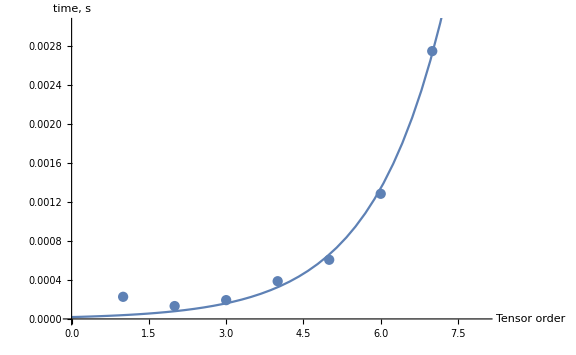

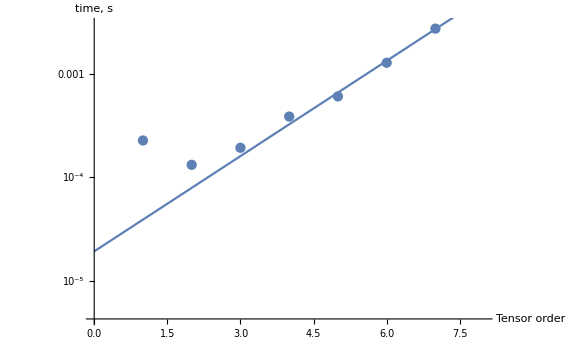

```mathematica
Table[Timing[ITensor[DummyArray[i]]][[1]],{i,1,7}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

C tensor.

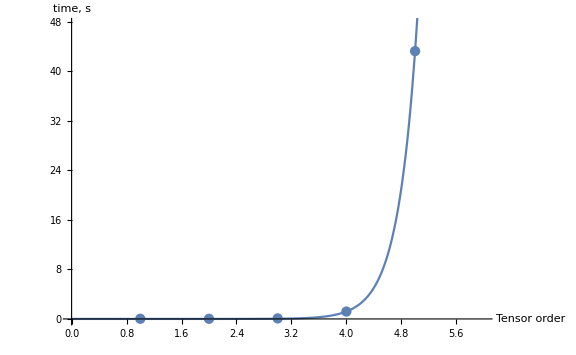

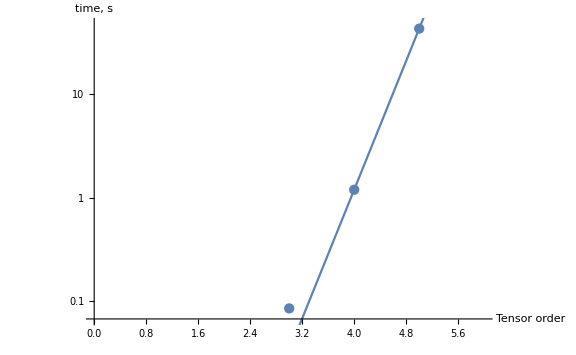

```mathematica
Table[Timing[CTensor[DummyArray[i]]][[1]],{i,1,5}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

CIII tensor.

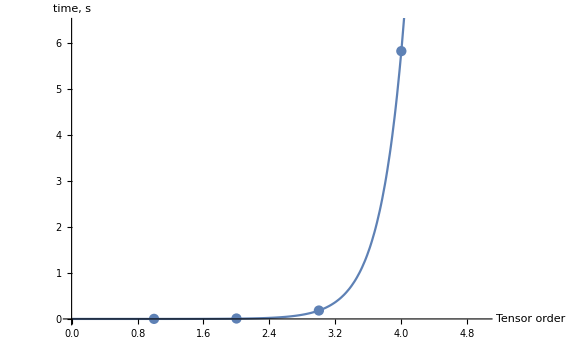

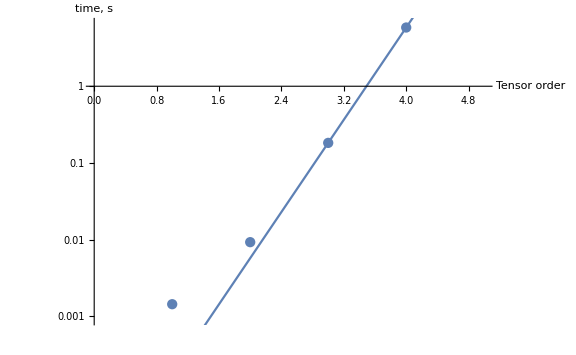

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[i]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton vertex.

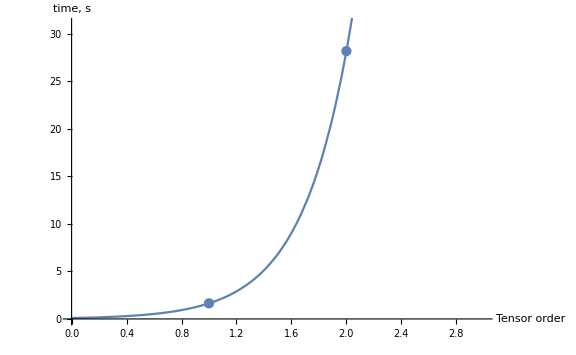

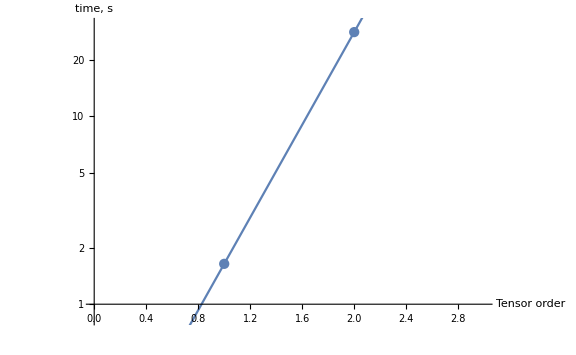

```mathematica
Table[Timing[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[i]]]][[1]],{i,3,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-scalar vertex.

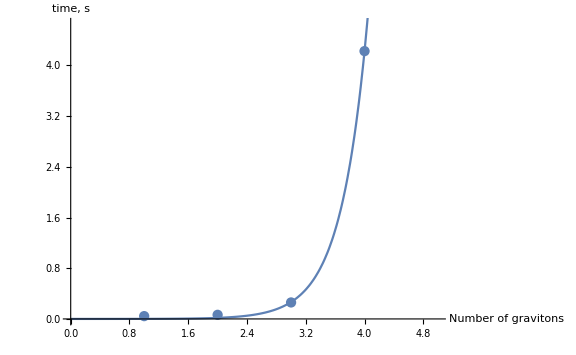

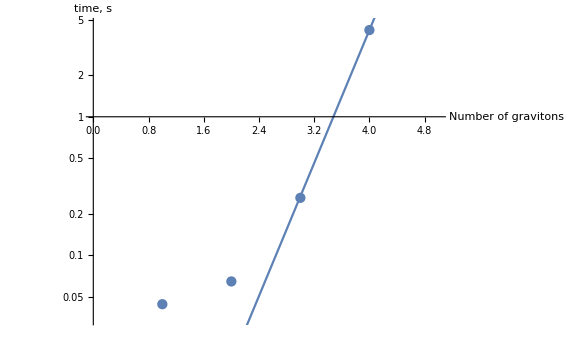

```mathematica
Table[Timing[GravitonScalarVertex[Join[dummyArray[i],{p1,p2}]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-vector vertex.

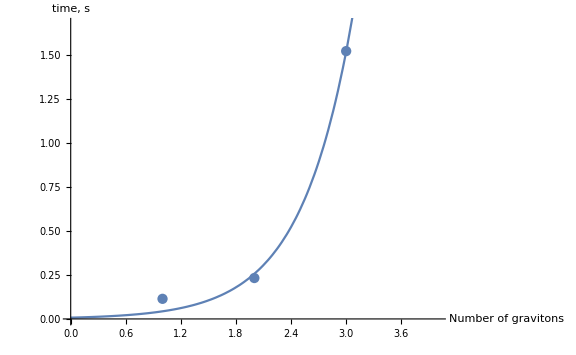

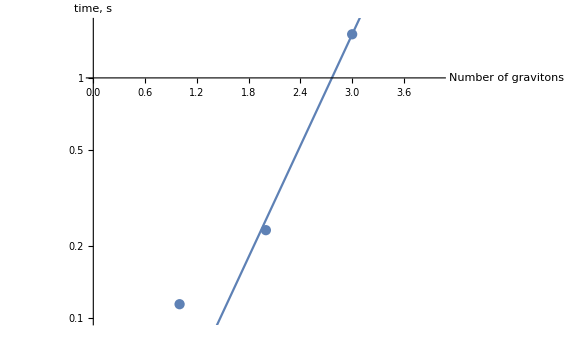

```mathematica
Table[Timing[GravitonVectorVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-fermion vertex.

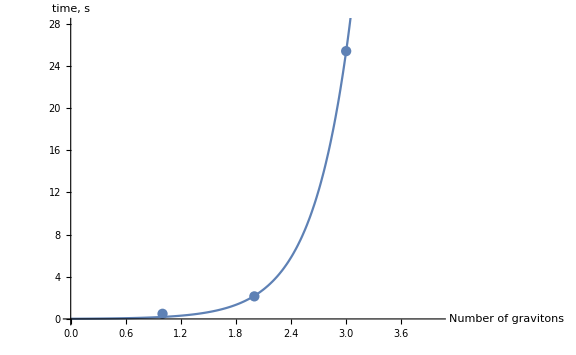

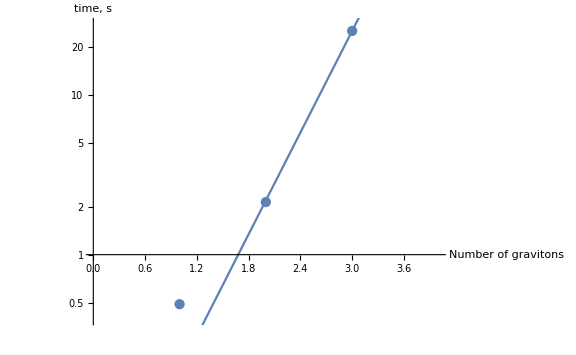

```mathematica
Table[Timing[GravitonFermionVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

# Export procedures.

```mathematica
<<FeynCalc`
<<DummyArray`
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<ETensor`
<<CETensor`
<<GravitonVertex`
<<GravitonScalarVertex`
<<GravitonFermionVertex`
```

## Procedures that perform export of interaction vertices.

This command set the working directory to be the directory where this file is placed.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/latosh_boris/.Mathematica/Applications/FeynGrav/Libs

Export of graviton vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVertex[order_] := Module[{cursor}, 
Print["Export of graviton vertices is initiated."];
For[cursor=3,cursor≤order+2,cursor++,
Evaluate[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[cursor]]]]>>"GravitonVertex_"<>ToString[cursor-2];
Print["Done for order "<>ToString[cursor-2]];
]
]
```

Export of graviton-scalar vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonScalarVertex[order_]:=Module[{cursor},
Print["Export of graviton-scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonScalarVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonMassiveScalarVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
]
```

Export of graviton-vector vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVectorVertex[order_]:=Module[{cursor},
	Print["Export of graviton-vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}]]]>>"GravitonVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}],m]]>>"GravitonMassiveVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

Export of graviton-fermion vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonFermionVertex[order_]:=Module[{cursor},
	Print["Export of graviton-fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonFermionVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-massive fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveFermionVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

Export of graviton-SU(N)YM vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonSUNYMVertex[order_]:=Module[{cursor},
	Print["Export of graviton-quark-gluon vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonQuarkGluonVertex[Join[dummyArray[cursor],{μ,a}]]]>>"GravitonQuarkGluonVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-three-gluon vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonThreeGluonVertex[Join[dummyArray[cursor],{p1,μ1,a1,p2,μ2,a2,p3,μ3,a3}]]]>>"GravitonThreeGluonVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-four-gluon vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonFourGluonVertex[Join[dummyArray[cursor],{p1,μ1,a1,p2,μ2,a2,p3,μ3,a3,p4,μ4,a4}]]]>>"GravitonFourGluonVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

## The actual export. Do not run without a necessity!

The following module runs the export procedure. The export is performed up to the order 𝒪(κ^order).

```mathematica
Module[{order},
order =3;
exportGravitonVertex[order];
exportGravitonScalarVertex[order];
exportGravitonVectorVertex[order];
exportGravitonFermionVertex[order];
exportGravitonSUNYMVertex[order];
]
```